One should first read the general file Roots@WeightsModele (or the particular file B2Roots&Weights) and then, the particular file B2level k, for each section devoted to level k.

Modify the name used in  SetDirectory for all sections ADE - A2Graphs -> ADE - GGraphs and more generally A2 (or whatever) by appropriate name

### General simplify trigo

```mathematica
Unprotect[Cos,Sin];
```

```mathematica
Cos[Pi/8]=(√(2+√2))/2;
Sin[Pi/8]=(√(2-√2))/2;
```

```mathematica
Protect[Cos,Sin];
```

### k=1 OK

```mathematica
SetDirectory["/Users/g5/Documents/MyMathematicaPrograms/ADE-E6Graphs"]
```

/Users/g5/Documents/MyMathematicaPrograms/ADE-E6Graphs

```mathematica
integrableweights=<<"Irreplist-level-1.m" (* may be useless since Irreplist[k] is recalculated *)
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0}}

```mathematica
fusionmatrixlist=<< "Fusion-A-level-1.m"
```

{SparseArray[<3>,{3,3}],SparseArray[<3>,{3,3}],SparseArray[<3>,{3,3}]}

```mathematica
fusionmatrixlist[[1]]//Normal
```

{{1,0,0},{0,1,0},{0,0,1}}

#### General stuff

```mathematica
holdpow[x__]:=HoldForm[Power[x]]
```

```mathematica
fundamentalIrreplist[k_]:=Prepend[Select[Irreplist[k],Apply[Plus,#]== 1 &],ConstantArray[0,r]]
(* all fundamental irreps may not be integrable at the chosen level. This list has the ordering induced from Irreplist[k]  *)
```

#### Information that will be used in labeling

```mathematica
k
```

1

```mathematica
Irreplist[k]
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0}}

```mathematica
fundamentalIrreplist[k]
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0}}

```mathematica
basicpositions =Flatten[ Table[Position[Irreplist[k],Drop[fundamentalIrreplist[k],1][[s]]],{s,1 ,r}]]
(* positions of fundamental integrable irreps in Irreplist *)
```

Part::partw: Part 3 of {{0, 0, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 0}} does not exist.

Part::partw: Part 4 of {{0, 0, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 0}} does not exist.

Part::partw: Part 5 of {{0, 0, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 0}} does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

{2,3}

```mathematica
λmax[k]
```

3

```mathematica
Map[dimensionOfIrrep, Irreplist[k]]//tonumbers // FullSimplify
```

{1,27,27}

```mathematica
Map[qdimensionOfIrrep, Irreplist[k]]//tonumbers // FullSimplify
```

{1,1,1}

```mathematica
(* cardA[k_]:=cardA[k]=Module[{qdimlis=Map[qdimensionOfIrrep,Irreplist[k]]}, qdimlis.qdimlis ] *)(* the sum of the squares of the dimensions of the integrable representations *)
```

```mathematica
cardA[k]//tonumbers // FullSimplify
```

3

```mathematica
κ
```

13

```mathematica
TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]]
```

Altitude is 12+1 = 13 , so q^13==-1

```mathematica
horizontaldimensions=Apply[Plus,Map[Normal,fusionmatrixlist],2]
```

{3,3,3}

```mathematica
totalhorizontaldimension=Apply[Plus,horizontaldimensions]
```

9

```mathematica
bialgebradimension = horizontaldimensions.horizontaldimensions
```

27

```mathematica
Apply[holdpow,FactorInteger[bialgebradimension],1]
```

{3^3}

```mathematica
fusiontitle=TextCell[Column[{"E6",StringJoin["Level ",ToString[k]],"", TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]]}]]
```

E6
Level 1

Altitude is 12+1 = 13 , so q^13==-1

```mathematica
fusiontitle=TextCell[Column[{
Style["E6",Large],
Style[StringJoin["Level ",ToString[k]],Large],
"",
 TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]],
 TextCell[Row[{"Central charge : ",CentralCharge }]],
"",
TextCell[Row[{
Style[Text["Quantum cardinal : "],Larger,Blue],
Text[FullSimplify[tonumbers[cardA[k]]]]}]]
}]]
```

E6
Level 1

Altitude is 12+1 = 13 , so q^13==-1
Central charge : 6

Quantum cardinal : 3

```mathematica
Mod[Map[h,toWeights[Irreplist[k]]],1]
```

{0,2/3,2/3}

```mathematica
integrableweightslabel=TextCell[Column[{
TextCell[Row[{
Style[Text["Integrable weights at this level : "],Larger,Blue],
Text[λmax[k]],
Text[" (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :"] }]],
Text[Irreplist[k],BaseStyle->{Red,Medium}],
Text[ FullSimplify[tonumbers[Map[dimensionOfIrrep,Irreplist[k]]]],BaseStyle->{Black,Medium}],
Text[ FullSimplify[tonumbers[Map[qdimensionOfIrrep,Irreplist[k]]]],BaseStyle->{Red,Medium}],
Text[Map[h,toWeights[Irreplist[k]]],BaseStyle->{Black,Medium}],
Text[Mod[Map[h,toWeights[Irreplist[k]]],1],BaseStyle->{Black,Medium}]
}],Background->LightGray,CellFrame->True]
```

Integrable weights at this level : 3 (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0}}
{1,27,27}
{1,1,1}
{0,2/3,2/3}
{0,2/3,2/3}

```mathematica
quantumgroupoidlabel=TextCell[Column[{
Style[Text["Quantum groupoid :"],Larger,Blue],
TextCell[Row[{"Size of blocks : ",horizontaldimensions}],BaseStyle->{Blue,Medium}],
TextCell[Row[{"Total horizontal dimension : ",totalhorizontaldimension}],BaseStyle->{Blue,Medium}],
TextCell[Row[{
"Bialgebra dimension : ",bialgebradimension," = ",Apply[Times, Apply[holdpow,FactorInteger[bialgebradimension],1]]}],BaseStyle->{Blue,Medium}]
}],Background->LightGray,CellFrame->True]
```

Quantum groupoid :
Size of blocks : {3,3,3}
Total horizontal dimension : 9
Bialgebra dimension : 27 = 3^3

```mathematica
integrablefundamentalweightslabel=TextCell[Column[{
TextCell[Row[{
Style[Text["Integrable fundamental weights"],Larger,Blue],
Text[" (list, classical dimensions, quantum dimensions) :"] }]],
Text[fundamentalIrreplist[k],BaseStyle->{Red,Medium}],
Text[ FullSimplify[tonumbers[Map[dimensionOfIrrep, fundamentalIrreplist[k]]]],BaseStyle->{Black,Medium}],
Text[ FullSimplify[tonumbers[Map[qdimensionOfIrrep,fundamentalIrreplist[k]]]],BaseStyle->{Red,Medium}]
}],Background->LightGray,CellFrame->True]
```

Integrable fundamental weights (list, classical dimensions, quantum dimensions) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0}}
{1,27,27}
{1,1,1}

```mathematica
Map[h,toWeights[Irreplist[k]]]
```

{0,2/3,2/3}

#### Build labeled picture

```mathematica
magnifactor=1.0;
```

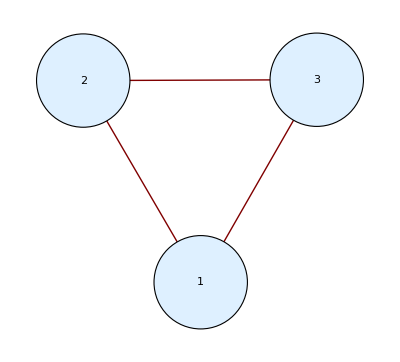
-Graphics-F_{0,0,0,0,1,0}
-Graphics-F_{1,0,0,0,0,0}E6
Level 1

Altitude is 12+1 = 13 , so q^13==-1
Central charge : 6

Quantum cardinal : 3Integrable weights at this level : 3 (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0}}
{1,27,27}
{1,1,1}
{0,2/3,2/3}
{0,2/3,2/3}Quantum groupoid :
Size of blocks : {3,3,3}
Total horizontal dimension : 9
Bialgebra dimension : 27 = 3^3Integrable fundamental weights (list, classical dimensions, quantum dimensions) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0}}
{1,27,27}
{1,1,1}

```mathematica
Labeled[TableForm[Table[Magnify[Labeled[Framed[GraphPlot[ fusionmatrixlist[[s]], VertexRenderingFunction -> ({LightBlue, EdgeForm[Black], Disk[#,.2], Black, Text[#2,#1]}&) , DirectedEdges -> True, MultiedgeStyle->True,SelfLoopStyle->True],Background->LightPurple],Text[Subscript["F",Irreplist[k][[s]]],BaseStyle->{Larger}]   , Left,ImageSize-> Full],magnifactor],{s,basicpositions }]],
{fusiontitle ,Text[integrableweightslabel],quantumgroupoidlabel,integrablefundamentalweightslabel},
{Left,Bottom,Right,Top},
FrameMargins->50]
```

### k=2 OK

```mathematica
SetDirectory["/Users/g5/Documents/MyMathematicaPrograms/ADE-E6Graphs"]
```

/Users/g5/Documents/MyMathematicaPrograms/ADE-E6Graphs

```mathematica
"/Users/g5/Documents/MyMathematicaPrograms/ADE-E6Graphs"
```

/Users/g5/Documents/MyMathematicaPrograms/ADE-E6Graphs

Evaluate file E6levelk and modify names of the next two external files

```mathematica
integrableweights=<<"Irreplist-level-2.m" (* may be useless since Irreplist[k] is recalculated *)
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0}}

```mathematica
fusionmatrixlist=<< "Fusion-A-level-2.m"
```

{SparseArray[<9>,{9,9}],SparseArray[<18>,{9,9}],SparseArray[<18>,{9,9}],SparseArray[<15>,{9,9}],SparseArray[<9>,{9,9}],SparseArray[<15>,{9,9}],SparseArray[<15>,{9,9}],SparseArray[<18>,{9,9}],SparseArray[<9>,{9,9}]}

#### General stuff

```mathematica
holdpow[x__]:=HoldForm[Power[x]]
```

```mathematica
fundamentalIrreplist[k_]:=Prepend[Select[Irreplist[k],Apply[Plus,#]== 1 &],ConstantArray[0,r]]
(* all fundamental irreps may not be integrable at the chosen level. This list has the ordering induced from Irreplist[k]  *)
```

#### Information that will be used in labeling

```mathematica
k
```

2

```mathematica
Irreplist[k]
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0}}

```mathematica
fundamentalIrreplist[k]
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,1,0,0,0,0}}

```mathematica
basicpositions =Flatten[ Table[Position[Irreplist[k],Drop[fundamentalIrreplist[k],1][[s]]],{s,1 ,r}]]
(* positions of fundamental integrable irreps in Irreplist *)
```

Part::partw: Part 6 of {{0, 0, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 0}} does not exist.

{2,3,4,6,7}

```mathematica
λmax[k]
```

9

```mathematica
Map[dimensionOfIrrep, Irreplist[k]]//tonumbers // FullSimplify
```

{1,27,27,78,351,351,351,650,351}

```mathematica
Map[qdimensionOfIrrep, Irreplist[k]]//tonumbers // FullSimplify
```

{1,1+(-1)^(2/7)-(-1)^(5/7),1+(-1)^(2/7)-(-1)^(5/7),(-1)^(1/7)-(-1)^(6/7),1,Root[1-2 #1-#1^2+#1^3&,3],Root[1-2 #1-#1^2+#1^3&,3],Root[1-#1-2 #1^2+#1^3&,3],1}

```mathematica
cardA[k]//tonumbers // FullSimplify
```

3 Root[-49+49 #1-14 #1^2+#1^3&,3]

```mathematica
κ
```

14

```mathematica
TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]]
```

Altitude is 12+2 = 14 , so q^14==-1

```mathematica
horizontaldimensions=Apply[Plus,Map[Normal,fusionmatrixlist],2]
```

{9,18,18,15,9,15,15,18,9}

```mathematica
totalhorizontaldimension=Apply[Plus,horizontaldimensions]
```

126

```mathematica
bialgebradimension = horizontaldimensions.horizontaldimensions
```

1890

```mathematica
Apply[holdpow,FactorInteger[bialgebradimension],1]
```

{2^1,3^3,5^1,7^1}

```mathematica
fusiontitle=TextCell[Column[{"E6",StringJoin["Level ",ToString[k]],"", TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]]}]]
```

E6
Level 2

Altitude is 12+2 = 14 , so q^14==-1

```mathematica
fusiontitle=TextCell[Column[{
Style["E6",Large],
Style[StringJoin["Level ",ToString[k]],Large],
"",
 TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]],
 TextCell[Row[{"Central charge : ",CentralCharge }]],
"",
TextCell[Row[{
Style[Text["Quantum cardinal : "],Larger,Blue],
Text[FullSimplify[tonumbers[cardA[k]]]]}]]
}]]
```

E6
Level 2

Altitude is 12+2 = 14 , so q^14==-1
Central charge : 78/7

Quantum cardinal : 3 Root[-49+49 #1-14 #1^2+#1^3&,3]

```mathematica
Mod[Map[h,toWeights[Irreplist[k]]],1]
```

{0,13/21,13/21,6/7,1/3,4/21,4/21,2/7,1/3}

```mathematica
integrableweightslabel=TextCell[Column[{
TextCell[Row[{
Style[Text["Integrable weights at this level :"],Larger,Blue],
Text[λmax[k]],
Text[" (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :"] }]],
Text[Irreplist[k],BaseStyle->{Red,Medium}],
Text[ FullSimplify[tonumbers[Map[dimensionOfIrrep,Irreplist[k]]]],BaseStyle->{Black,Medium}],
Text[ FullSimplify[tonumbers[Map[qdimensionOfIrrep,Irreplist[k]]]],BaseStyle->{Red,Medium}],
Text[Map[h,toWeights[Irreplist[k]]],BaseStyle->{Black,Medium}],
Text[Mod[Map[h,toWeights[Irreplist[k]]],1],BaseStyle->{Black,Medium}]
}],Background->LightGray,CellFrame->True]
```

Integrable weights at this level :9 (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0}}
{1,27,27,78,351,351,351,650,351}
{1,1+(-1)^(2/7)-(-1)^(5/7),1+(-1)^(2/7)-(-1)^(5/7),(-1)^(1/7)-(-1)^(6/7),1,Root[1-2 #1-#1^2+#1^3&,3],Root[1-2 #1-#1^2+#1^3&,3],Root[1-#1-2 #1^2+#1^3&,3],1}
{0,13/21,13/21,6/7,4/3,25/21,25/21,9/7,4/3}
{0,13/21,13/21,6/7,1/3,4/21,4/21,2/7,1/3}

```mathematica
quantumgroupoidlabel=TextCell[Column[{
Style[Text["Quantum groupoid :"],Larger,Blue],
TextCell[Row[{"Size of blocks : ",horizontaldimensions}],BaseStyle->{Blue,Medium}],
TextCell[Row[{"Total horizontal dimension : ",totalhorizontaldimension}],BaseStyle->{Blue,Medium}],
TextCell[Row[{
"Bialgebra dimension : ",bialgebradimension," = ",Apply[Times, Apply[holdpow,FactorInteger[bialgebradimension],1]]}],BaseStyle->{Blue,Medium}]
}],Background->LightGray,CellFrame->True]
```

Quantum groupoid :
Size of blocks : {9,18,18,15,9,15,15,18,9}
Total horizontal dimension : 126
Bialgebra dimension : 1890 = 2^1 3^3 5^1 7^1

```mathematica
integrablefundamentalweightslabel=TextCell[Column[{
TextCell[Row[{
Style[Text["Integrable fundamental weights"],Larger,Blue],
Text[" (list, classical dimensions, quantum dimensions) :"] }]],
Text[fundamentalIrreplist[k],BaseStyle->{Red,Medium}],
Text[ FullSimplify[tonumbers[Map[dimensionOfIrrep, fundamentalIrreplist[k]]]],BaseStyle->{Black,Medium}],
Text[ FullSimplify[tonumbers[Map[qdimensionOfIrrep,fundamentalIrreplist[k]]]],BaseStyle->{Red,Medium}]
}],Background->LightGray,CellFrame->True]
```

Integrable fundamental weights (list, classical dimensions, quantum dimensions) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,1,0,0,0,0}}
{1,27,27,78,351,351}
{1,1+(-1)^(2/7)-(-1)^(5/7),1+(-1)^(2/7)-(-1)^(5/7),(-1)^(1/7)-(-1)^(6/7),Root[1-2 #1-#1^2+#1^3&,3],Root[1-2 #1-#1^2+#1^3&,3]}

```mathematica
Map[h,toWeights[Irreplist[k]]]
```

{0,13/21,13/21,6/7,4/3,25/21,25/21,9/7,4/3}

#### Build labeled picture

```mathematica
magnifactor=1.0;
```

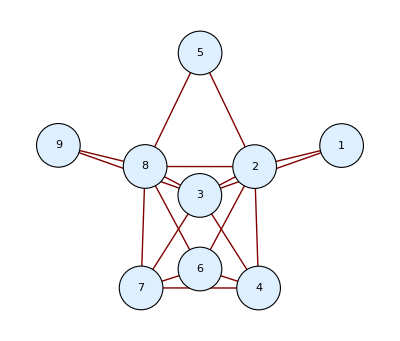
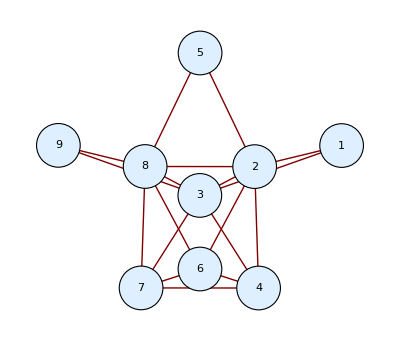
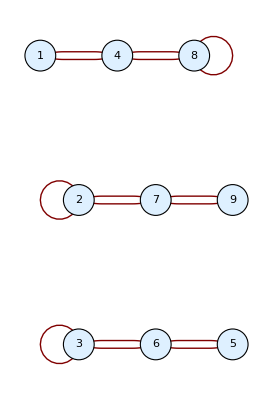
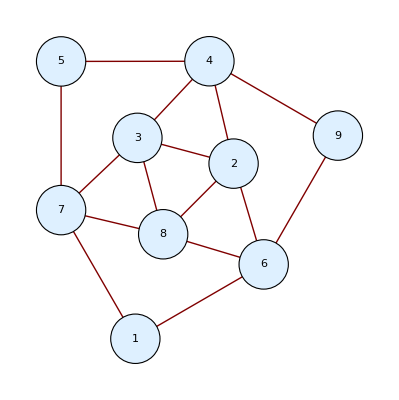
-Graphics-F_{0,0,0,0,1,0}
-Graphics-F_{1,0,0,0,0,0}
-Graphics-F_{0,0,0,0,0,1}
-Graphics-F_{0,0,0,1,0,0}
-Graphics-F_{0,1,0,0,0,0}E6
Level 2

Altitude is 12+2 = 14 , so q^14==-1
Central charge : 78/7

Quantum cardinal : 3 Root[-49+49 #1-14 #1^2+#1^3&,3]Integrable weights at this level :9 (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0}}
{1,27,27,78,351,351,351,650,351}
{1,1+(-1)^(2/7)-(-1)^(5/7),1+(-1)^(2/7)-(-1)^(5/7),(-1)^(1/7)-(-1)^(6/7),1,Root[1-2 #1-#1^2+#1^3&,3],Root[1-2 #1-#1^2+#1^3&,3],Root[1-#1-2 #1^2+#1^3&,3],1}
{0,13/21,13/21,6/7,4/3,25/21,25/21,9/7,4/3}
{0,13/21,13/21,6/7,1/3,4/21,4/21,2/7,1/3}Quantum groupoid :
Size of blocks : {9,18,18,15,9,15,15,18,9}
Total horizontal dimension : 126
Bialgebra dimension : 1890 = 2^1 3^3 5^1 7^1Integrable fundamental weights (list, classical dimensions, quantum dimensions) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,1,0,0,0,0}}
{1,27,27,78,351,351}
{1,1+(-1)^(2/7)-(-1)^(5/7),1+(-1)^(2/7)-(-1)^(5/7),(-1)^(1/7)-(-1)^(6/7),Root[1-2 #1-#1^2+#1^3&,3],Root[1-2 #1-#1^2+#1^3&,3]}

```mathematica
Labeled[TableForm[Table[Magnify[Labeled[Framed[GraphPlot[ fusionmatrixlist[[s]], VertexRenderingFunction -> ({LightBlue, EdgeForm[Black], Disk[#,.2], Black, Text[#2,#1]}&) , DirectedEdges -> True, MultiedgeStyle->True,SelfLoopStyle->True],Background->LightPurple],Text[Subscript["F",Irreplist[k][[s]]],BaseStyle->{Larger}]   , Left,ImageSize-> Full],magnifactor],{s,basicpositions }]],
{fusiontitle ,Text[integrableweightslabel],quantumgroupoidlabel,integrablefundamentalweightslabel},
{Left,Bottom,Right,Top},
FrameMargins->50]
```

### k=3 OK

```mathematica
SetDirectory["/Users/g5/Documents/MyMathematicaPrograms/ADE-E6Graphs"]
```

/Users/g5/Documents/MyMathematicaPrograms/ADE-E6Graphs

Evaluate file E6levelk and modify names of the next two external files

```mathematica
integrableweights=<<"Irreplist-level-3.m" (* may be useless since Irreplist[k] is recalculated *)
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0},{0,0,0,0,1,1},{0,0,0,0,3,0},{0,0,0,1,1,0},{0,0,1,0,0,0},{0,1,0,0,1,0},{1,0,0,0,0,1},{1,0,0,0,2,0},{1,0,0,1,0,0},{1,1,0,0,0,0},{2,0,0,0,1,0},{3,0,0,0,0,0}}

```mathematica
fusionmatrixlist=<< "Fusion-A-level-3.m"
```

{SparseArray[<20>,{20,20}],SparseArray[<63>,{20,20}],SparseArray[<63>,{20,20}],SparseArray[<72>,{20,20}],SparseArray[<63>,{20,20}],SparseArray[<90>,{20,20}],SparseArray[<90>,{20,20}],SparseArray[<103>,{20,20}],SparseArray[<63>,{20,20}],SparseArray[<90>,{20,20}],SparseArray[<20>,{20,20}],SparseArray[<72>,{20,20}],SparseArray[<79>,{20,20}],SparseArray[<90>,{20,20}],SparseArray[<90>,{20,20}],SparseArray[<63>,{20,20}],SparseArray[<90>,{20,20}],SparseArray[<72>,{20,20}],SparseArray[<63>,{20,20}],SparseArray[<20>,{20,20}]}

#### General stuff

```mathematica
holdpow[x__]:=HoldForm[Power[x]]
```

```mathematica
fundamentalIrreplist[k_]:=Prepend[Select[Irreplist[k],Apply[Plus,#]== 1 &],ConstantArray[0,r]]
(* all fundamental irreps may not be integrable at the chosen level. This list has the ordering induced from Irreplist[k]  *)
```

#### Information that will be used in labeling

```mathematica
k
```

3

```mathematica
Irreplist[k]
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0},{0,0,0,0,1,1},{0,0,0,0,3,0},{0,0,0,1,1,0},{0,0,1,0,0,0},{0,1,0,0,1,0},{1,0,0,0,0,1},{1,0,0,0,2,0},{1,0,0,1,0,0},{1,1,0,0,0,0},{2,0,0,0,1,0},{3,0,0,0,0,0}}

```mathematica
fundamentalIrreplist[k]
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0}}

```mathematica
basicpositions =Flatten[ Table[Position[Irreplist[k],Drop[fundamentalIrreplist[k],1][[s]]],{s,1 ,r}]]
(* positions of fundamental integrable irreps in Irreplist *)
```

{2,3,4,6,7,13}

```mathematica
λmax[k]
```

20

```mathematica
Map[dimensionOfIrrep, Irreplist[k]]//tonumbers // FullSimplify
```

{1,27,27,78,351,351,351,650,351,1728,3003,5824,2925,7371,1728,7722,7371,5824,7722,3003}

```mathematica
Map[qdimensionOfIrrep, Irreplist[k]]//tonumbers // FullSimplify
```

{1,1/2 (5+√5),1/2 (5+√5),2+√5,1/2 (5+√5),1/2 (5+3 √5),1/2 (5+3 √5),3/2 (3+√5),1/2 (5+√5),1/2 (5+3 √5),1,2+√5,Cos[π/15] Root[331776+13824 #1-2304 #1^2-96 #1^3+#1^4&,4] Sin[π/15]^2,1/2 (5+3 √5),1/2 (5+3 √5),1/2 (5+√5),1/2 (5+3 √5),2+√5,1/2 (5+√5),1}

```mathematica
cardA[k]//tonumbers // FullSimplify
```

45 (5+2 √5)

```mathematica
κ
```

15

```mathematica
TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]]
```

Altitude is 12+3 = 15 , so q^15==-1

```mathematica
horizontaldimensions=Apply[Plus,Map[Normal,fusionmatrixlist],2]
```

{20,63,63,73,63,99,99,132,63,99,20,73,82,99,99,63,99,73,63,20}

```mathematica
totalhorizontaldimension=Apply[Plus,horizontaldimensions]
```

1465

```mathematica
bialgebradimension = horizontaldimensions.horizontaldimensions
```

123955

```mathematica
Apply[holdpow,FactorInteger[bialgebradimension],1]
```

{5^1,13^1,1907^1}

```mathematica
fusiontitle=TextCell[Column[{"E6",StringJoin["Level ",ToString[k]],"", TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]]}]]
```

E6
Level 3

Altitude is 12+3 = 15 , so q^15==-1

```mathematica
fusiontitle=TextCell[Column[{
Style["E6",Large],
Style[StringJoin["Level ",ToString[k]],Large],
"",
 TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]],
 TextCell[Row[{"Central charge : ",CentralCharge }]],
"",
TextCell[Row[{
Style[Text["Quantum cardinal : "],Larger,Blue],
Text[FullSimplify[tonumbers[cardA[k]]]]}]]
}]]
```

E6
Level 3

Altitude is 12+3 = 15 , so q^15==-1
Central charge : 78/5

Quantum cardinal : 45 (5+2 √5)

```mathematica
Mod[Map[h,toWeights[Irreplist[k]]],1]
```

{0,26/45,26/45,4/5,11/45,1/9,1/9,1/5,11/45,4/9,0,4/5,3/5,7/9,4/9,41/45,7/9,4/5,41/45,0}

```mathematica
integrableweightslabel=TextCell[Column[{
TextCell[Row[{
Style[Text["Integrable weights at this level :"],Larger,Blue],
Text[λmax[k]],
Text[" (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :"] }]],
Text[Irreplist[k],BaseStyle->{Red,Medium}],
Text[ FullSimplify[tonumbers[Map[dimensionOfIrrep,Irreplist[k]]]],BaseStyle->{Black,Medium}],
Text[ FullSimplify[tonumbers[Map[qdimensionOfIrrep,Irreplist[k]]]],BaseStyle->{Red,Medium}],
Text[Map[h,toWeights[Irreplist[k]]],BaseStyle->{Black,Medium}],
Text[Mod[Map[h,toWeights[Irreplist[k]]],1],BaseStyle->{Black,Medium}]
}],Background->LightGray,CellFrame->True]
```

Integrable weights at this level :20 (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0},{0,0,0,0,1,1},{0,0,0,0,3,0},{0,0,0,1,1,0},{0,0,1,0,0,0},{0,1,0,0,1,0},{1,0,0,0,0,1},{1,0,0,0,2,0},{1,0,0,1,0,0},{1,1,0,0,0,0},{2,0,0,0,1,0},{3,0,0,0,0,0}}
{1,27,27,78,351,351,351,650,351,1728,3003,5824,2925,7371,1728,7722,7371,5824,7722,3003}
{1,1/2 (5+√5),1/2 (5+√5),2+√5,1/2 (5+√5),1/2 (5+3 √5),1/2 (5+3 √5),3/2 (3+√5),1/2 (5+√5),1/2 (5+3 √5),1,2+√5,Cos[π/15] Root[331776+13824 #1-2304 #1^2-96 #1^3+#1^4&,4] Sin[π/15]^2,1/2 (5+3 √5),1/2 (5+3 √5),1/2 (5+√5),1/2 (5+3 √5),2+√5,1/2 (5+√5),1}
{0,26/45,26/45,4/5,56/45,10/9,10/9,6/5,56/45,13/9,2,9/5,8/5,16/9,13/9,86/45,16/9,9/5,86/45,2}
{0,26/45,26/45,4/5,11/45,1/9,1/9,1/5,11/45,4/9,0,4/5,3/5,7/9,4/9,41/45,7/9,4/5,41/45,0}

```mathematica
quantumgroupoidlabel=TextCell[Column[{
Style[Text["Quantum groupoid :"],Larger,Blue],
TextCell[Row[{"Size of blocks : ",horizontaldimensions}],BaseStyle->{Blue,Medium}],
TextCell[Row[{"Total horizontal dimension : ",totalhorizontaldimension}],BaseStyle->{Blue,Medium}],
TextCell[Row[{
"Bialgebra dimension : ",bialgebradimension," = ",Apply[Times, Apply[holdpow,FactorInteger[bialgebradimension],1]]}],BaseStyle->{Blue,Medium}]
}],Background->LightGray,CellFrame->True]
```

Quantum groupoid :
Size of blocks : {20,63,63,73,63,99,99,132,63,99,20,73,82,99,99,63,99,73,63,20}
Total horizontal dimension : 1465
Bialgebra dimension : 123955 = 5^1 13^1 1907^1

```mathematica
integrablefundamentalweightslabel=TextCell[Column[{
TextCell[Row[{
Style[Text["Integrable fundamental weights"],Larger,Blue],
Text[" (list, classical dimensions, quantum dimensions) :"] }]],
Text[fundamentalIrreplist[k],BaseStyle->{Red,Medium}],
Text[ FullSimplify[tonumbers[Map[dimensionOfIrrep, fundamentalIrreplist[k]]]],BaseStyle->{Black,Medium}],
Text[ FullSimplify[tonumbers[Map[qdimensionOfIrrep,fundamentalIrreplist[k]]]],BaseStyle->{Red,Medium}]
}],Background->LightGray,CellFrame->True]
```

Integrable fundamental weights :20 (list, classical dimensions, quantum dimensions) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0}}
{1,27,27,78,351,351,2925}
{1,1/2 (5+√5),1/2 (5+√5),2+√5,1/2 (5+3 √5),1/2 (5+3 √5),Cos[π/15] Root[331776+13824 #1-2304 #1^2-96 #1^3+#1^4&,4] Sin[π/15]^2}

```mathematica
Map[h,toWeights[Irreplist[k]]]
```

{0,26/45,26/45,4/5,56/45,10/9,10/9,6/5,56/45,13/9,2,9/5,8/5,16/9,13/9,86/45,16/9,9/5,86/45,2}

#### Build labeled picture

```mathematica
magnifactor=1.0;
```

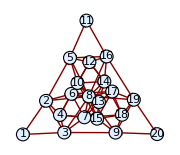
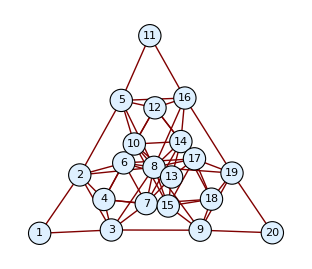
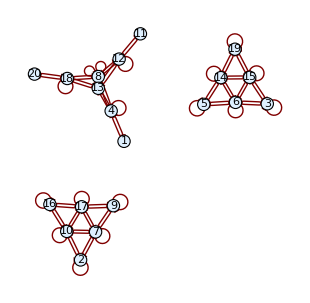
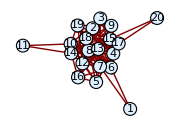
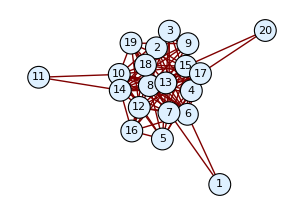
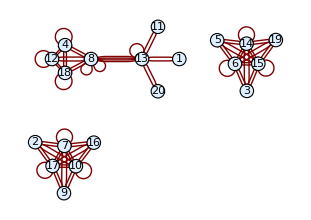
-Graphics-F_{0,0,0,0,1,0}
-Graphics-F_{1,0,0,0,0,0}
-Graphics-F_{0,0,0,0,0,1}
-Graphics-F_{0,0,0,1,0,0}
-Graphics-F_{0,1,0,0,0,0}
-Graphics-F_{0,0,1,0,0,0}E6
Level 3

Altitude is 12+3 = 15 , so q^15==-1
Central charge : 78/5

Quantum cardinal : 45 (5+2 √5)Integrable weights at this level :20 (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0},{0,0,0,0,1,1},{0,0,0,0,3,0},{0,0,0,1,1,0},{0,0,1,0,0,0},{0,1,0,0,1,0},{1,0,0,0,0,1},{1,0,0,0,2,0},{1,0,0,1,0,0},{1,1,0,0,0,0},{2,0,0,0,1,0},{3,0,0,0,0,0}}
{1,27,27,78,351,351,351,650,351,1728,3003,5824,2925,7371,1728,7722,7371,5824,7722,3003}
{1,1/2 (5+√5),1/2 (5+√5),2+√5,1/2 (5+√5),1/2 (5+3 √5),1/2 (5+3 √5),3/2 (3+√5),1/2 (5+√5),1/2 (5+3 √5),1,2+√5,Cos[π/15] Root[331776+13824 #1-2304 #1^2-96 #1^3+#1^4&,4] Sin[π/15]^2,1/2 (5+3 √5),1/2 (5+3 √5),1/2 (5+√5),1/2 (5+3 √5),2+√5,1/2 (5+√5),1}
{0,26/45,26/45,4/5,56/45,10/9,10/9,6/5,56/45,13/9,2,9/5,8/5,16/9,13/9,86/45,16/9,9/5,86/45,2}
{0,26/45,26/45,4/5,11/45,1/9,1/9,1/5,11/45,4/9,0,4/5,3/5,7/9,4/9,41/45,7/9,4/5,41/45,0}Quantum groupoid :
Size of blocks : {20,63,63,73,63,99,99,132,63,99,20,73,82,99,99,63,99,73,63,20}
Total horizontal dimension : 1465
Bialgebra dimension : 123955 = 5^1 13^1 1907^1Integrable fundamental weights :20 (list, classical dimensions, quantum dimensions) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0}}
{1,27,27,78,351,351,2925}
{1,1/2 (5+√5),1/2 (5+√5),2+√5,1/2 (5+3 √5),1/2 (5+3 √5),Cos[π/15] Root[331776+13824 #1-2304 #1^2-96 #1^3+#1^4&,4] Sin[π/15]^2}

```mathematica
Labeled[TableForm[Table[Magnify[Labeled[Framed[GraphPlot[ fusionmatrixlist[[s]], VertexRenderingFunction -> ({LightBlue, EdgeForm[Black], Disk[#,.2], Black, Text[#2,#1]}&) , DirectedEdges -> True, MultiedgeStyle->True,SelfLoopStyle->True],Background->LightPurple],Text[Subscript["F",Irreplist[k][[s]]],BaseStyle->{Larger}]   , Left,ImageSize-> Full],magnifactor],{s,basicpositions }]],
{fusiontitle ,Text[integrableweightslabel],quantumgroupoidlabel,integrablefundamentalweightslabel},
{Left,Bottom,Right,Top},
FrameMargins->50]
```

### k=4 STRANGE: does not seem to agree with previous calculations on laptop

```mathematica
SetDirectory["/Users/g5/Documents/MyMathematicaPrograms/ADE-E6Graphs"]
```

/Users/g5/Documents/MyMathematicaPrograms/ADE-E6Graphs

Evaluate file E6levelk and modify names of the next two external files

```mathematica
integrableweights=<<"Irreplist-level-4.m" (* may be useless since Irreplist[k] is recalculated *)
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0},{0,0,0,0,1,1},{0,0,0,0,3,0},{0,0,0,1,1,0},{0,0,1,0,0,0},{0,1,0,0,1,0},{1,0,0,0,0,1},{1,0,0,0,2,0},{1,0,0,1,0,0},{1,1,0,0,0,0},{2,0,0,0,1,0},{3,0,0,0,0,0},{0,0,0,0,0,2},{0,0,0,0,2,1},{0,0,0,0,4,0},{0,0,0,1,0,1},{0,0,0,1,2,0},{0,0,0,2,0,0},{0,0,1,0,1,0},{0,1,0,0,0,1},{0,1,0,0,2,0},{0,1,0,1,0,0},{0,2,0,0,0,0},{1,0,0,0,1,1},{1,0,0,0,3,0},{1,0,0,1,1,0},{1,0,1,0,0,0},{1,1,0,0,1,0},{2,0,0,0,0,1},{2,0,0,0,2,0},{2,0,0,1,0,0},{2,1,0,0,0,0},{3,0,0,0,1,0},{4,0,0,0,0,0}}

```mathematica
fusionmatrixlist=<< "Fusion-A-level-4.m"
```

{SparseArray[<42>,{42,42}],SparseArray[<174>,{42,42}],SparseArray[<174>,{42,42}],SparseArray[<228>,{42,42}],SparseArray[<252>,{42,42}],SparseArray[<318>,{42,42}],SparseArray[<318>,{42,42}],SparseArray[<381>,{42,42}],SparseArray[<252>,{42,42}],SparseArray[<387>,{42,42}],SparseArray[<174>,{42,42}],SparseArray[<387>,{42,42}],SparseArray[<387>,{42,42}],SparseArray[<447>,{42,42}],SparseArray[<387>,{42,42}],SparseArray[<381>,{42,42}],SparseArray[<447>,{42,42}],SparseArray[<387>,{42,42}],SparseArray[<381>,{42,42}],SparseArray[<174>,{42,42}],SparseArray[<231>,{42,42}],SparseArray[<318>,{42,42}],SparseArray[<42>,{42,42}],SparseArray[<375>,{42,42}],SparseArray[<228>,{42,42}],SparseArray[<231>,{42,42}],SparseArray[<387>,{42,42}],SparseArray[<375>,{42,42}],SparseArray[<318>,{42,42}],SparseArray[<375>,{42,42}],SparseArray[<231>,{42,42}],SparseArray[<447>,{42,42}],SparseArray[<174>,{42,42}],SparseArray[<387>,{42,42}],SparseArray[<387>,{42,42}],SparseArray[<387>,{42,42}],SparseArray[<318>,{42,42}],SparseArray[<252>,{42,42}],SparseArray[<318>,{42,42}],SparseArray[<228>,{42,42}],SparseArray[<174>,{42,42}],SparseArray[<42>,{42,42}]}

#### General stuff

```mathematica
holdpow[x__]:=HoldForm[Power[x]]
```

```mathematica
fundamentalIrreplist[k_]:=Prepend[Select[Irreplist[k],Apply[Plus,#]== 1 &],ConstantArray[0,r]]
(* all fundamental irreps may not be integrable at the chosen level. This list has the ordering induced from Irreplist[k]  *)
```

#### Information that will be used in labeling

```mathematica
k
```

4

```mathematica
Irreplist[k]
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0},{0,0,0,0,1,1},{0,0,0,0,3,0},{0,0,0,1,1,0},{0,0,1,0,0,0},{0,1,0,0,1,0},{1,0,0,0,0,1},{1,0,0,0,2,0},{1,0,0,1,0,0},{1,1,0,0,0,0},{2,0,0,0,1,0},{3,0,0,0,0,0},{0,0,0,0,0,2},{0,0,0,0,2,1},{0,0,0,0,4,0},{0,0,0,1,0,1},{0,0,0,1,2,0},{0,0,0,2,0,0},{0,0,1,0,1,0},{0,1,0,0,0,1},{0,1,0,0,2,0},{0,1,0,1,0,0},{0,2,0,0,0,0},{1,0,0,0,1,1},{1,0,0,0,3,0},{1,0,0,1,1,0},{1,0,1,0,0,0},{1,1,0,0,1,0},{2,0,0,0,0,1},{2,0,0,0,2,0},{2,0,0,1,0,0},{2,1,0,0,0,0},{3,0,0,0,1,0},{4,0,0,0,0,0}}

```mathematica
fundamentalIrreplist[k]
```

{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0}}

```mathematica
basicpositions =Flatten[ Table[Position[Irreplist[k],Drop[fundamentalIrreplist[k],1][[s]]],{s,1 ,r}]]
(* positions of fundamental integrable irreps in Irreplist *)
```

{2,3,4,6,7,13}

```mathematica
λmax[k]
```

42

```mathematica
Map[dimensionOfIrrep, Irreplist[k]]//tonumbers // FullSimplify
```

{1,27,27,78,351,351,351,650,351,1728,3003,5824,2925,7371,1728,7722,7371,5824,7722,3003,2430,19305,19305,17550,54054,34398,51975,17550,78975,70070,34398,34749,61425,112320,51975,112320,19305,85293,78975,54054,61425,19305}

```mathematica
Map[qdimensionOfIrrep, Irreplist[k]]//tonumbers // FullSimplify
```

{1,1+√2+√(2 (2+√2)),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+√2+2 √(2+√2),3+2 √2+√(20+14 √2),3+2 √2+√(20+14 √2),4+3 √2+2 √(10+7 √2),3+√2+2 √(2+√2),2 (2+2 √2+√(10+7 √2)),1+√2+√(2 (2+√2)),2 (2+2 √2+√(10+7 √2)),5+3 √2+2 √(10+7 √2),7+4 √2+2 √(20+14 √2),2 (2+2 √2+√(10+7 √2)),4+3 √2+2 √(10+7 √2),7+4 √2+2 √(20+14 √2),2 (2+2 √2+√(10+7 √2)),4+3 √2+2 √(10+7 √2),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+2 √2+√(20+14 √2),1,4+3 √2+2 √(10+7 √2),2+√2+2 √(2+√2),2+√2+2 √(2+√2),5+3 √2+2 √(10+7 √2),4+3 √2+2 √(10+7 √2),3+2 √2+√(20+14 √2),4+3 √2+2 √(10+7 √2),2+√2+2 √(2+√2),7+4 √2+2 √(20+14 √2),1+√2+√(2 (2+√2)),2 (2+2 √2+√(10+7 √2)),5+3 √2+2 √(10+7 √2),2 (2+2 √2+√(10+7 √2)),3+2 √2+√(20+14 √2),3+√2+2 √(2+√2),3+2 √2+√(20+14 √2),2+√2+2 √(2+√2),1+√2+√(2 (2+√2)),1}

```mathematica
cardA[k]
```

1+(2 9_q^2 12_q^2)/(1_q^2 4_q^2)+(8_q^2 9_q^2 13_q^2)/(1_q^2 3_q^2 4_q^2)+(2 6_q^2 9_q^2 12_q^2 13_q^2)/(1_q^2 2_q^2 3_q^2 4_q^2)+(5_q^2 8_q^2 10_q^2 12_q^2 13_q^2)/(1_q^4 4_q^4 6_q^2)+(2 9_q^2 10_q^2 12_q^2 13_q^2)/(1_q^2 2_q^2 4_q^2 5_q^2)+(2 6_q^2 8_q^2 9_q^2 10_q^2 12_q^2 14_q^2)/(1_q^4 3_q^2 4_q^2 5_q^2 7_q^2)+(5_q^2 9_q^4 10_q^2 13_q^2 14_q^2)/(1_q^2 2_q^4 3_q^4 7_q^2)+(2 9_q^4 12_q^2 13_q^2 14_q^2)/(1_q^4 2_q^2 3_q^2 4_q^2)+(2 6_q^2 8_q^2 10_q^2 12_q^2 13_q^2 14_q^2)/(1_q^4 3_q^4 4_q^2 5_q^2)+(2 8_q^2 9_q^2 11_q^2 12_q^2 13_q^2 14_q^2)/(1_q^4 2_q^2 4_q^4 7_q^2)+(2 9_q^2 10_q^2 11_q^2 12_q^2 13_q^2 14_q^2)/(1_q^2 2_q^2 3_q^2 4_q^2 5_q^2 6_q^2)+(8_q^2 9_q^4 10_q^2 12_q^2 15_q^2)/(1_q^2 2_q^2 3_q^2 4_q^4 5_q^2)+(2 8_q^2 9_q^2 10_q^2 12_q^2 13_q^2 15_q^2)/(1_q^4 2_q^2 3_q^2 4_q^4)+(9_q^4 11_q^2 12_q^2 13_q^2 15_q^2)/(1_q^6 3_q^2 4_q^2 5_q^2)+(2 9_q^2 10_q^2 11_q^2 12_q^2 13_q^2 15_q^2)/(1_q^4 2_q^2 3_q^2 4_q^2 5_q^2)+(2 9_q^2 10_q^2 11_q^2 12_q^2 14_q^2 15_q^2)/(1_q^4 2_q^4 3_q^2 4_q^2)+(7_q^2 8_q^2 10_q^2 11_q^2 13_q^2 14_q^2 15_q^2)/(1_q^4 2_q^4 3_q^2 4_q^2 5_q^2)+(2 6_q^2 7_q^2 8_q^2 9_q^2 12_q^2 13_q^2 14_q^2 15_q^2)/(1_q^2 2_q^4 3_q^4 4_q^4 5_q^2)+(2 6_q^2 8_q^2 9_q^2 10_q^2 12_q^2 13_q^2 14_q^2 15_q^2)/(1_q^6 3_q^4 4_q^2 5_q^2 7_q^2)+(2 9_q^4 10_q^2 12_q^2 13_q^2 14_q^2 15_q^2)/(1_q^4 2_q^4 3_q^2 4_q^2 7_q^2)+(2 8_q^2 9_q^2 11_q^2 12_q^2 13_q^2 14_q^2 15_q^2)/(1_q^4 2_q^2 3_q^2 4_q^4 5_q^2)+(6_q^2 9_q^4 12_q^4 13_q^2 14_q^2 15_q^2)/(1_q^4 2_q^4 4_q^4 5_q^2 7_q^2)+(2 9_q^2 10_q^2 12_q^4 13_q^2 14_q^2 15_q^2)/(1_q^4 2_q^2 3_q^2 4_q^4 6_q^2)+(2 9_q^2 10_q^2 11_q^2 12_q^4 13_q^2 14_q^2 15_q^2)/(1_q^2 2_q^2 3_q^2 4_q^4 5_q^2 6_q^2 7_q^2)

```mathematica
cardA[k]//tonumbers // FullSimplify
```

96 (22+15 √2+4 √(58+41 √2))

```mathematica
κ
```

16

```mathematica
TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]]
```

Altitude is 12+4 = 16 , so q^16==-1

```mathematica
horizontaldimensions=Apply[Plus,Map[Normal,fusionmatrixlist],2]
```

{42,174,174,240,270,396,396,558,270,600,174,600,582,810,600,558,810,600,558,174,234,396,42,552,240,234,582,552,396,552,234,810,174,600,582,600,396,270,396,240,174,42}

```mathematica
totalhorizontaldimension=Apply[Plus,horizontaldimensions]
```

16884

```mathematica
bialgebradimension = horizontaldimensions.horizontaldimensions
```

8676288

```mathematica
Apply[holdpow,FactorInteger[bialgebradimension],1]
```

{2^6,3^3,5021^1}

```mathematica
fusiontitle=TextCell[Column[{"E6",StringJoin["Level ",ToString[k]],"", TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]]}]]
```

E6
Level 4

Altitude is 12+4 = 16 , so q^16==-1

```mathematica
fusiontitle=TextCell[Column[{
Style["E6",Large],
Style[StringJoin["Level ",ToString[k]],Large],
"",
 TextCell[Row[{StringJoin["Altitude is ", ToString[HoldForm[Evaluate[g]]],"+",ToString[ HoldForm[Evaluate[k]]]," = ",ToString[κ]," , so "],q^κ ==-1}]],
 TextCell[Row[{"Central charge : ",CentralCharge }]],
"",
TextCell[Row[{
Style[Text["Quantum cardinal : "],Larger,Blue],
Text[FullSimplify[tonumbers[cardA[k]]]]}]]
}]]
```

E6
Level 4

Altitude is 12+4 = 16 , so q^16==-1
Central charge : 39/2

Quantum cardinal : 96 (22+15 √2+4 √(58+41 √2))

```mathematica
Mod[Map[h,toWeights[Irreplist[k]]],1]
```

{0,4/15,2/5,2/5,4/15,28/45,11/15,32/45,5/9,14/15,8/9,32/45,14/15,11/15,28/45,1/15,7/45,1/9,14/15,1/3,4/15,1/15,13/45,1/15,14/15,3/5,23/45,13/45,23/45,4/15,1/9,3/5,1/3,7/45,1/15,3/5,2/3,3/5,2/5,37/45,11/15,23/45,11/15,22/45,1/3,1/15,43/45,32/45,14/15,2/3,22/45,0,32/45,23/45,2/5,2/5,4/15,0,2/9,14/15,11/15,4/15,43/45,11/15,3/5,2/5,1/15,37/45,2/3,3/5}

```mathematica
integrableweightslabel=TextCell[Column[{
TextCell[Row[{
Style[Text["Integrable weights at this level :"],Larger,Blue],
Text[λmax[k]],
Text[" (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :"] }]],
Text[Irreplist[k],BaseStyle->{Red,Medium}],
Text[ FullSimplify[tonumbers[Map[dimensionOfIrrep,Irreplist[k]]]],BaseStyle->{Black,Medium}],
Text[ FullSimplify[tonumbers[Map[qdimensionOfIrrep,Irreplist[k]]]],BaseStyle->{Red,Medium}],
Text[Map[h,toWeights[Irreplist[k]]],BaseStyle->{Black,Medium}],
Text[Mod[Map[h,toWeights[Irreplist[k]]],1],BaseStyle->{Black,Medium}]
}],Background->LightGray,CellFrame->True]
```

Integrable weights at this level :42 (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0},{0,0,0,0,1,1},{0,0,0,0,3,0},{0,0,0,1,1,0},{0,0,1,0,0,0},{0,1,0,0,1,0},{1,0,0,0,0,1},{1,0,0,0,2,0},{1,0,0,1,0,0},{1,1,0,0,0,0},{2,0,0,0,1,0},{3,0,0,0,0,0},{0,0,0,0,0,2},{0,0,0,0,2,1},{0,0,0,0,4,0},{0,0,0,1,0,1},{0,0,0,1,2,0},{0,0,0,2,0,0},{0,0,1,0,1,0},{0,1,0,0,0,1},{0,1,0,0,2,0},{0,1,0,1,0,0},{0,2,0,0,0,0},{1,0,0,0,1,1},{1,0,0,0,3,0},{1,0,0,1,1,0},{1,0,1,0,0,0},{1,1,0,0,1,0},{2,0,0,0,0,1},{2,0,0,0,2,0},{2,0,0,1,0,0},{2,1,0,0,0,0},{3,0,0,0,1,0},{4,0,0,0,0,0}}
{1,27,27,78,351,351,351,650,351,1728,3003,5824,2925,7371,1728,7722,7371,5824,7722,3003,2430,19305,19305,17550,54054,34398,51975,17550,78975,70070,34398,34749,61425,112320,51975,112320,19305,85293,78975,54054,61425,19305}
{1,1+√2+√(2 (2+√2)),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+√2+2 √(2+√2),3+2 √2+√(20+14 √2),3+2 √2+√(20+14 √2),4+3 √2+2 √(10+7 √2),3+√2+2 √(2+√2),2 (2+2 √2+√(10+7 √2)),1+√2+√(2 (2+√2)),2 (2+2 √2+√(10+7 √2)),5+3 √2+2 √(10+7 √2),7+4 √2+2 √(20+14 √2),2 (2+2 √2+√(10+7 √2)),4+3 √2+2 √(10+7 √2),7+4 √2+2 √(20+14 √2),2 (2+2 √2+√(10+7 √2)),4+3 √2+2 √(10+7 √2),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+2 √2+√(20+14 √2),1,4+3 √2+2 √(10+7 √2),2+√2+2 √(2+√2),2+√2+2 √(2+√2),5+3 √2+2 √(10+7 √2),4+3 √2+2 √(10+7 √2),3+2 √2+√(20+14 √2),4+3 √2+2 √(10+7 √2),2+√2+2 √(2+√2),7+4 √2+2 √(20+14 √2),1+√2+√(2 (2+√2)),2 (2+2 √2+√(10+7 √2)),5+3 √2+2 √(10+7 √2),2 (2+2 √2+√(10+7 √2)),3+2 √2+√(20+14 √2),3+√2+2 √(2+√2),3+2 √2+√(20+14 √2),2+√2+2 √(2+√2),1+√2+√(2 (2+√2)),1}
{0,13/24,13/24,3/4,7/6,25/24,25/24,9/8,7/6,65/48,15/8,27/16,3/2,5/3,65/48,43/24,5/3,27/16,43/24,15/8,13/8,49/24,8/3,23/12,29/12,55/24,13/6,23/12,19/8,9/4,55/24,2,61/24,113/48,13/6,113/48,49/24,5/2,19/8,29/12,61/24,8/3}
{0,13/24,13/24,3/4,1/6,1/24,1/24,1/8,1/6,17/48,7/8,11/16,1/2,2/3,17/48,19/24,2/3,11/16,19/24,7/8,5/8,1/24,2/3,11/12,5/12,7/24,1/6,11/12,3/8,1/4,7/24,0,13/24,17/48,1/6,17/48,1/24,1/2,3/8,5/12,13/24,2/3}

```mathematica
quantumgroupoidlabel=TextCell[Column[{
Style[Text["Quantum groupoid :"],Larger,Blue],
TextCell[Row[{"Size of blocks : ",horizontaldimensions}],BaseStyle->{Blue,Medium}],
TextCell[Row[{"Total horizontal dimension : ",totalhorizontaldimension}],BaseStyle->{Blue,Medium}],
TextCell[Row[{
"Bialgebra dimension : ",bialgebradimension," = ",Apply[Times, Apply[holdpow,FactorInteger[bialgebradimension],1]]}],BaseStyle->{Blue,Medium}]
}],Background->LightGray,CellFrame->True]
```

Quantum groupoid :
Size of blocks : {42,174,174,240,270,396,396,558,270,600,174,600,582,810,600,558,810,600,558,174,234,396,42,552,240,234,582,552,396,552,234,810,174,600,582,600,396,270,396,240,174,42}
Total horizontal dimension : 16884
Bialgebra dimension : 8676288 = 2^6 3^3 5021^1

```mathematica
integrablefundamentalweightslabel=TextCell[Column[{
TextCell[Row[{
Style[Text["Integrable fundamental weights"],Larger,Blue],
Text[" (list, classical dimensions, quantum dimensions) :"] }]],
Text[fundamentalIrreplist[k],BaseStyle->{Red,Medium}],
Text[ FullSimplify[tonumbers[Map[dimensionOfIrrep, fundamentalIrreplist[k]]]],BaseStyle->{Black,Medium}],
Text[ FullSimplify[tonumbers[Map[qdimensionOfIrrep,fundamentalIrreplist[k]]]],BaseStyle->{Red,Medium}]
}],Background->LightGray,CellFrame->True]
```

Integrable fundamental weights (list, classical dimensions, quantum dimensions) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0}}
{1,27,27,78,351,351,2925}
{1,1+√2+√(2 (2+√2)),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+2 √2+√(20+14 √2),3+2 √2+√(20+14 √2),5+3 √2+2 √(10+7 √2)}

```mathematica
Map[h,toWeights[Irreplist[k]]]
```

{0,13/24,13/24,3/4,7/6,25/24,25/24,9/8,7/6,65/48,15/8,27/16,3/2,5/3,65/48,43/24,5/3,27/16,43/24,15/8,13/8,49/24,8/3,23/12,29/12,55/24,13/6,23/12,19/8,9/4,55/24,2,61/24,113/48,13/6,113/48,49/24,5/2,19/8,29/12,61/24,8/3}

#### Build labeled picture

```mathematica
magnifactor=1.0;
```

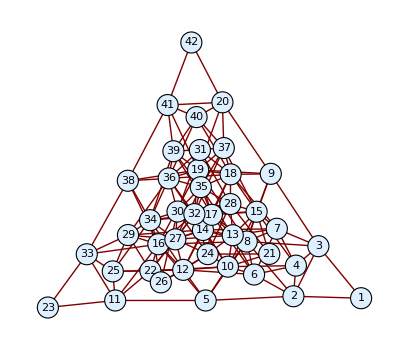
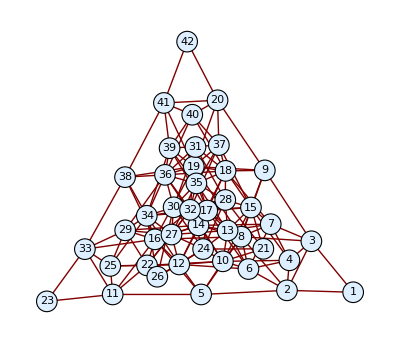
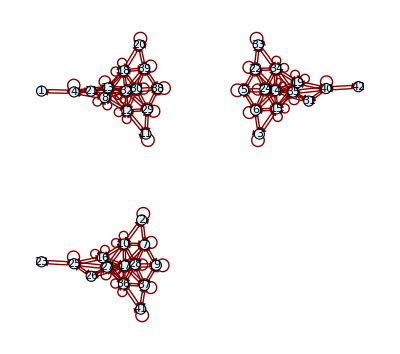
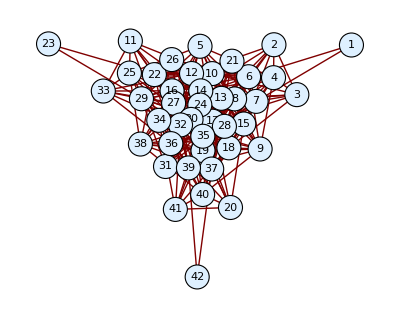
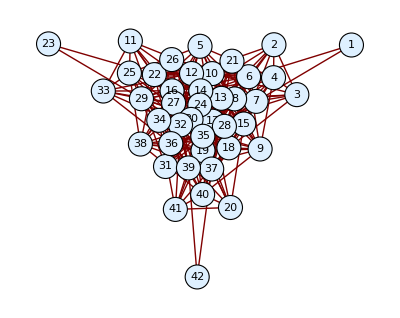
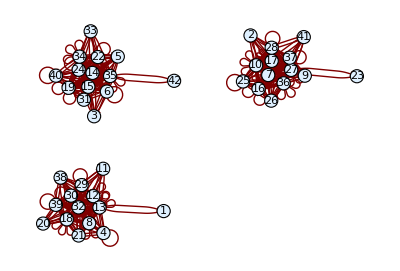
-Graphics-F_{0,0,0,0,1,0}
-Graphics-F_{1,0,0,0,0,0}
-Graphics-F_{0,0,0,0,0,1}
-Graphics-F_{0,0,0,1,0,0}
-Graphics-F_{0,1,0,0,0,0}
-Graphics-F_{0,0,1,0,0,0}E6
Level 4

Altitude is 12+4 = 16 , so q^16==-1
Central charge : 39/2

Quantum cardinal : 96 (22+15 √2+4 √(58+41 √2))Integrable weights at this level :42 (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0},{0,0,0,0,1,1},{0,0,0,0,3,0},{0,0,0,1,1,0},{0,0,1,0,0,0},{0,1,0,0,1,0},{1,0,0,0,0,1},{1,0,0,0,2,0},{1,0,0,1,0,0},{1,1,0,0,0,0},{2,0,0,0,1,0},{3,0,0,0,0,0},{0,0,0,0,0,2},{0,0,0,0,2,1},{0,0,0,0,4,0},{0,0,0,1,0,1},{0,0,0,1,2,0},{0,0,0,2,0,0},{0,0,1,0,1,0},{0,1,0,0,0,1},{0,1,0,0,2,0},{0,1,0,1,0,0},{0,2,0,0,0,0},{1,0,0,0,1,1},{1,0,0,0,3,0},{1,0,0,1,1,0},{1,0,1,0,0,0},{1,1,0,0,1,0},{2,0,0,0,0,1},{2,0,0,0,2,0},{2,0,0,1,0,0},{2,1,0,0,0,0},{3,0,0,0,1,0},{4,0,0,0,0,0}}
{1,27,27,78,351,351,351,650,351,1728,3003,5824,2925,7371,1728,7722,7371,5824,7722,3003,2430,19305,19305,17550,54054,34398,51975,17550,78975,70070,34398,34749,61425,112320,51975,112320,19305,85293,78975,54054,61425,19305}
{1,1+√2+√(2 (2+√2)),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+√2+2 √(2+√2),3+2 √2+√(20+14 √2),3+2 √2+√(20+14 √2),4+3 √2+2 √(10+7 √2),3+√2+2 √(2+√2),2 (2+2 √2+√(10+7 √2)),1+√2+√(2 (2+√2)),2 (2+2 √2+√(10+7 √2)),5+3 √2+2 √(10+7 √2),7+4 √2+2 √(20+14 √2),2 (2+2 √2+√(10+7 √2)),4+3 √2+2 √(10+7 √2),7+4 √2+2 √(20+14 √2),2 (2+2 √2+√(10+7 √2)),4+3 √2+2 √(10+7 √2),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+2 √2+√(20+14 √2),1,4+3 √2+2 √(10+7 √2),2+√2+2 √(2+√2),2+√2+2 √(2+√2),5+3 √2+2 √(10+7 √2),4+3 √2+2 √(10+7 √2),3+2 √2+√(20+14 √2),4+3 √2+2 √(10+7 √2),2+√2+2 √(2+√2),7+4 √2+2 √(20+14 √2),1+√2+√(2 (2+√2)),2 (2+2 √2+√(10+7 √2)),5+3 √2+2 √(10+7 √2),2 (2+2 √2+√(10+7 √2)),3+2 √2+√(20+14 √2),3+√2+2 √(2+√2),3+2 √2+√(20+14 √2),2+√2+2 √(2+√2),1+√2+√(2 (2+√2)),1}
{0,13/24,13/24,3/4,7/6,25/24,25/24,9/8,7/6,65/48,15/8,27/16,3/2,5/3,65/48,43/24,5/3,27/16,43/24,15/8,13/8,49/24,8/3,23/12,29/12,55/24,13/6,23/12,19/8,9/4,55/24,2,61/24,113/48,13/6,113/48,49/24,5/2,19/8,29/12,61/24,8/3}
{0,13/24,13/24,3/4,1/6,1/24,1/24,1/8,1/6,17/48,7/8,11/16,1/2,2/3,17/48,19/24,2/3,11/16,19/24,7/8,5/8,1/24,2/3,11/12,5/12,7/24,1/6,11/12,3/8,1/4,7/24,0,13/24,17/48,1/6,17/48,1/24,1/2,3/8,5/12,13/24,2/3}Quantum groupoid :
Size of blocks : {42,174,174,240,270,396,396,558,270,600,174,600,582,810,600,558,810,600,558,174,234,396,42,552,240,234,582,552,396,552,234,810,174,600,582,600,396,270,396,240,174,42}
Total horizontal dimension : 16884
Bialgebra dimension : 8676288 = 2^6 3^3 5021^1Integrable fundamental weights (list, classical dimensions, quantum dimensions) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0}}
{1,27,27,78,351,351,2925}
{1,1+√2+√(2 (2+√2)),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+2 √2+√(20+14 √2),3+2 √2+√(20+14 √2),5+3 √2+2 √(10+7 √2)}

```mathematica
Labeled[TableForm[Table[Magnify[Labeled[Framed[GraphPlot[ fusionmatrixlist[[s]], VertexRenderingFunction -> ({LightBlue, EdgeForm[Black], Disk[#,.20], Black, Text[#2,#1]}&) , DirectedEdges -> True, MultiedgeStyle->True,SelfLoopStyle->True],Background->LightPurple],Text[Subscript["F",Irreplist[k][[s]]],BaseStyle->{Larger}]   , Left,ImageSize-> Full],magnifactor],{s,basicpositions }]],
{fusiontitle ,Text[integrableweightslabel],quantumgroupoidlabel,integrablefundamentalweightslabel},
{Left,Bottom,Right,Top}]
```

```mathematica
Labeled[TableForm[Table[Magnify[Labeled[Framed[GraphPlot[ fusionmatrixlist[[s]], VertexRenderingFunction -> ({LightBlue, EdgeForm[Black], Disk[#,.20], Black, Text[#2,#1]}&) , DirectedEdges -> True, MultiedgeStyle->True,SelfLoopStyle->True],Background->LightPurple],Text[Subscript["F",Irreplist[k][[s]]],BaseStyle->{Larger}]   , Left,ImageSize-> Full],magnifactor],{s,basicpositions }]],
{fusiontitle ,Text[integrableweightslabel],quantumgroupoidlabel,integrablefundamentalweightslabel},
{Left,Bottom,Right,Top},
FrameMargins->50]
```

-Graphics-F_{0,0,0,0,1,0}
-Graphics-F_{1,0,0,0,0,0}
-Graphics-F_{0,0,0,0,0,1}
-Graphics-F_{0,0,0,1,0,0}
-Graphics-F_{0,1,0,0,0,0}
-Graphics-F_{0,0,1,0,0,0}E6
Level 4

Altitude is 12+4 = 16 , so q^16==-1
Central charge : 39/2

Quantum cardinal : 96 (22+15 √2+4 √(58+41 √2))Integrable weights at this level :42 (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0},{0,0,0,0,1,1},{0,0,0,0,3,0},{0,0,0,1,1,0},{0,0,1,0,0,0},{0,1,0,0,1,0},{1,0,0,0,0,1},{1,0,0,0,2,0},{1,0,0,1,0,0},{1,1,0,0,0,0},{2,0,0,0,1,0},{3,0,0,0,0,0},{0,0,0,0,0,2},{0,0,0,0,2,1},{0,0,0,0,4,0},{0,0,0,1,0,1},{0,0,0,1,2,0},{0,0,0,2,0,0},{0,0,1,0,1,0},{0,1,0,0,0,1},{0,1,0,0,2,0},{0,1,0,1,0,0},{0,2,0,0,0,0},{1,0,0,0,1,1},{1,0,0,0,3,0},{1,0,0,1,1,0},{1,0,1,0,0,0},{1,1,0,0,1,0},{2,0,0,0,0,1},{2,0,0,0,2,0},{2,0,0,1,0,0},{2,1,0,0,0,0},{3,0,0,0,1,0},{4,0,0,0,0,0}}
{1,27,27,78,351,351,351,650,351,1728,3003,5824,2925,7371,1728,7722,7371,5824,7722,3003,2430,19305,19305,17550,54054,34398,51975,17550,78975,70070,34398,34749,61425,112320,51975,112320,19305,85293,78975,54054,61425,19305}
{1,1+√2+√(2 (2+√2)),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+√2+2 √(2+√2),3+2 √2+√(20+14 √2),3+2 √2+√(20+14 √2),4+3 √2+2 √(10+7 √2),3+√2+2 √(2+√2),2 (2+2 √2+√(10+7 √2)),1+√2+√(2 (2+√2)),2 (2+2 √2+√(10+7 √2)),5+3 √2+2 √(10+7 √2),7+4 √2+2 √(20+14 √2),2 (2+2 √2+√(10+7 √2)),4+3 √2+2 √(10+7 √2),7+4 √2+2 √(20+14 √2),2 (2+2 √2+√(10+7 √2)),4+3 √2+2 √(10+7 √2),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+2 √2+√(20+14 √2),1,4+3 √2+2 √(10+7 √2),2+√2+2 √(2+√2),2+√2+2 √(2+√2),5+3 √2+2 √(10+7 √2),4+3 √2+2 √(10+7 √2),3+2 √2+√(20+14 √2),4+3 √2+2 √(10+7 √2),2+√2+2 √(2+√2),7+4 √2+2 √(20+14 √2),1+√2+√(2 (2+√2)),2 (2+2 √2+√(10+7 √2)),5+3 √2+2 √(10+7 √2),2 (2+2 √2+√(10+7 √2)),3+2 √2+√(20+14 √2),3+√2+2 √(2+√2),3+2 √2+√(20+14 √2),2+√2+2 √(2+√2),1+√2+√(2 (2+√2)),1}
{0,13/24,13/24,3/4,7/6,25/24,25/24,9/8,7/6,65/48,15/8,27/16,3/2,5/3,65/48,43/24,5/3,27/16,43/24,15/8,13/8,49/24,8/3,23/12,29/12,55/24,13/6,23/12,19/8,9/4,55/24,2,61/24,113/48,13/6,113/48,49/24,5/2,19/8,29/12,61/24,8/3}
{0,13/24,13/24,3/4,1/6,1/24,1/24,1/8,1/6,17/48,7/8,11/16,1/2,2/3,17/48,19/24,2/3,11/16,19/24,7/8,5/8,1/24,2/3,11/12,5/12,7/24,1/6,11/12,3/8,1/4,7/24,0,13/24,17/48,1/6,17/48,1/24,1/2,3/8,5/12,13/24,2/3}Quantum groupoid :
Size of blocks : {42,174,174,240,270,396,396,558,270,600,174,600,582,810,600,558,810,600,558,174,234,396,42,552,240,234,582,552,396,552,234,810,174,600,582,600,396,270,396,240,174,42}
Total horizontal dimension : 16884
Bialgebra dimension : 8676288 = 2^6 3^3 5021^1Integrable fundamental weights (list, classical dimensions, quantum dimensions) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0}}
{1,27,27,78,351,351,2925}
{1,1+√2+√(2 (2+√2)),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+2 √2+√(20+14 √2),3+2 √2+√(20+14 √2),5+3 √2+2 √(10+7 √2)}

```mathematica
magnifactor=1.5;
```

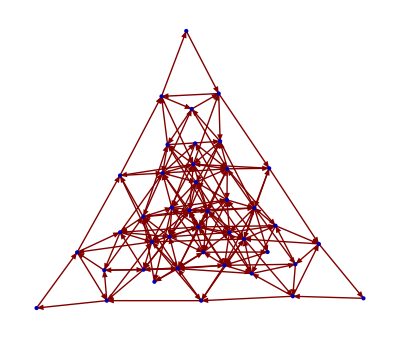
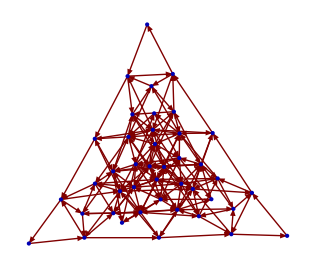
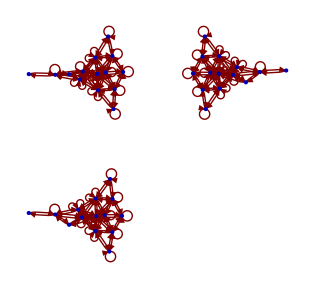
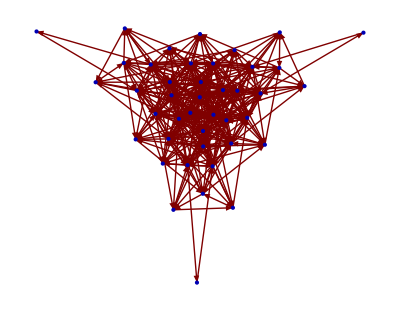
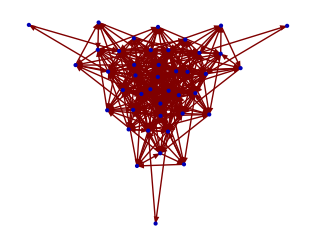
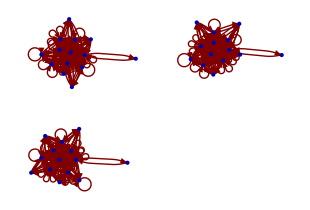
-Graphics-F_{0,0,0,0,1,0}
-Graphics-F_{1,0,0,0,0,0}
-Graphics-F_{0,0,0,0,0,1}
-Graphics-F_{0,0,0,1,0,0}
-Graphics-F_{0,1,0,0,0,0}
-Graphics-F_{0,0,1,0,0,0}E6
Level 4

Altitude is 12+4 = 16 , so q^16==-1
Central charge : 39/2

Quantum cardinal : 96 (22+15 √2+4 √(58+41 √2))Integrable weights at this level :42 (list, classical dimensions, quantum dimensions, conformal weights, reduced conformal weights mod 1) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,1,0,0},{0,1,0,0,0,0},{1,0,0,0,1,0},{2,0,0,0,0,0},{0,0,0,0,1,1},{0,0,0,0,3,0},{0,0,0,1,1,0},{0,0,1,0,0,0},{0,1,0,0,1,0},{1,0,0,0,0,1},{1,0,0,0,2,0},{1,0,0,1,0,0},{1,1,0,0,0,0},{2,0,0,0,1,0},{3,0,0,0,0,0},{0,0,0,0,0,2},{0,0,0,0,2,1},{0,0,0,0,4,0},{0,0,0,1,0,1},{0,0,0,1,2,0},{0,0,0,2,0,0},{0,0,1,0,1,0},{0,1,0,0,0,1},{0,1,0,0,2,0},{0,1,0,1,0,0},{0,2,0,0,0,0},{1,0,0,0,1,1},{1,0,0,0,3,0},{1,0,0,1,1,0},{1,0,1,0,0,0},{1,1,0,0,1,0},{2,0,0,0,0,1},{2,0,0,0,2,0},{2,0,0,1,0,0},{2,1,0,0,0,0},{3,0,0,0,1,0},{4,0,0,0,0,0}}
{1,27,27,78,351,351,351,650,351,1728,3003,5824,2925,7371,1728,7722,7371,5824,7722,3003,2430,19305,19305,17550,54054,34398,51975,17550,78975,70070,34398,34749,61425,112320,51975,112320,19305,85293,78975,54054,61425,19305}
{1,1+√2+√(2 (2+√2)),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+√2+2 √(2+√2),3+2 √2+√(20+14 √2),3+2 √2+√(20+14 √2),4+3 √2+2 √(10+7 √2),3+√2+2 √(2+√2),2 (2+2 √2+√(10+7 √2)),1+√2+√(2 (2+√2)),2 (2+2 √2+√(10+7 √2)),5+3 √2+2 √(10+7 √2),7+4 √2+2 √(20+14 √2),2 (2+2 √2+√(10+7 √2)),4+3 √2+2 √(10+7 √2),7+4 √2+2 √(20+14 √2),2 (2+2 √2+√(10+7 √2)),4+3 √2+2 √(10+7 √2),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+2 √2+√(20+14 √2),1,4+3 √2+2 √(10+7 √2),2+√2+2 √(2+√2),2+√2+2 √(2+√2),5+3 √2+2 √(10+7 √2),4+3 √2+2 √(10+7 √2),3+2 √2+√(20+14 √2),4+3 √2+2 √(10+7 √2),2+√2+2 √(2+√2),7+4 √2+2 √(20+14 √2),1+√2+√(2 (2+√2)),2 (2+2 √2+√(10+7 √2)),5+3 √2+2 √(10+7 √2),2 (2+2 √2+√(10+7 √2)),3+2 √2+√(20+14 √2),3+√2+2 √(2+√2),3+2 √2+√(20+14 √2),2+√2+2 √(2+√2),1+√2+√(2 (2+√2)),1}
{0,13/24,13/24,3/4,7/6,25/24,25/24,9/8,7/6,65/48,15/8,27/16,3/2,5/3,65/48,43/24,5/3,27/16,43/24,15/8,13/8,49/24,8/3,23/12,29/12,55/24,13/6,23/12,19/8,9/4,55/24,2,61/24,113/48,13/6,113/48,49/24,5/2,19/8,29/12,61/24,8/3}
{0,13/24,13/24,3/4,1/6,1/24,1/24,1/8,1/6,17/48,7/8,11/16,1/2,2/3,17/48,19/24,2/3,11/16,19/24,7/8,5/8,1/24,2/3,11/12,5/12,7/24,1/6,11/12,3/8,1/4,7/24,0,13/24,17/48,1/6,17/48,1/24,1/2,3/8,5/12,13/24,2/3}Quantum groupoid :
Size of blocks : {42,174,174,240,270,396,396,558,270,600,174,600,582,810,600,558,810,600,558,174,234,396,42,552,240,234,582,552,396,552,234,810,174,600,582,600,396,270,396,240,174,42}
Total horizontal dimension : 16884
Bialgebra dimension : 8676288 = 2^6 3^3 5021^1Integrable fundamental weights (list, classical dimensions, quantum dimensions) :
{{0,0,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,1,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0}}
{1,27,27,78,351,351,2925}
{1,1+√2+√(2 (2+√2)),1+√2+√(2 (2+√2)),2+√2+2 √(2+√2),3+2 √2+√(20+14 √2),3+2 √2+√(20+14 √2),5+3 √2+2 √(10+7 √2)}

```mathematica
Labeled[TableForm[Table[Magnify[Labeled[Framed[GraphPlot[ fusionmatrixlist[[s]], DirectedEdges -> True, MultiedgeStyle->True,SelfLoopStyle->True],Background->LightPurple],Text[Subscript["F",Irreplist[k][[s]]],BaseStyle->{Larger}]   , Left,ImageSize-> Full],magnifactor],{s,basicpositions }]],
{fusiontitle ,Text[integrableweightslabel],quantumgroupoidlabel,integrablefundamentalweightslabel},
{Left,Bottom,Right,Top},
FrameMargins->50]
```

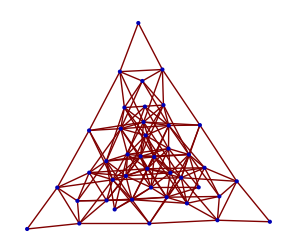
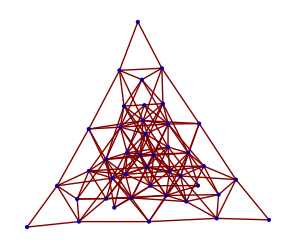
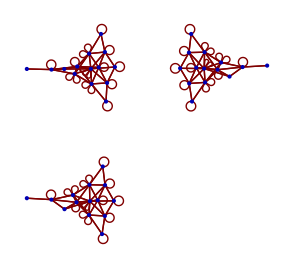
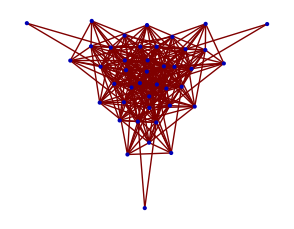
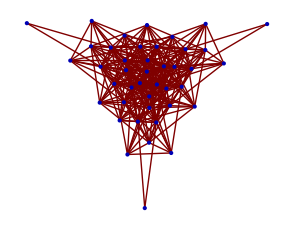
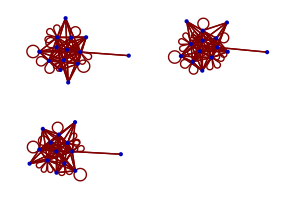
-Graphics-F_{0,0,0,0,1,0}
-Graphics-F_{1,0,0,0,0,0}
-Graphics-F_{0,0,0,0,0,1}
-Graphics-F_{0,0,0,1,0,0}
-Graphics-F_{0,1,0,0,0,0}
-Graphics-F_{0,0,1,0,0,0}

```mathematica
TableForm[Table[Magnify[Labeled[Framed[GraphPlot[ fusionmatrixlist[[s]] ,SelfLoopStyle->True],Background->LightPurple],Text[Subscript["F",Irreplist[k][[s]]],BaseStyle->{Larger}]   , Left,ImageSize-> Full],magnifactor],{s,basicpositions }]]
```

```mathematica
magnifactor=1.3;
```

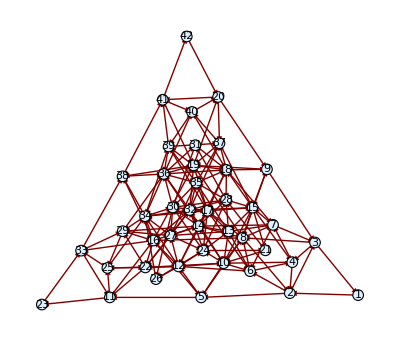
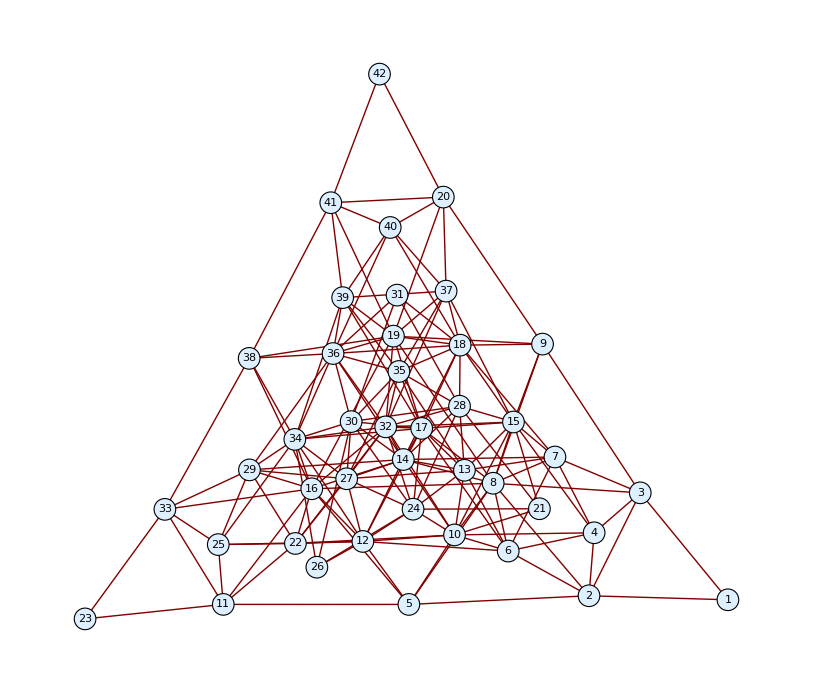
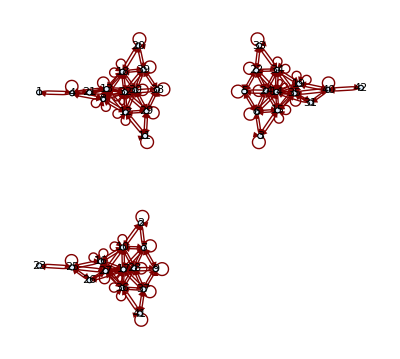
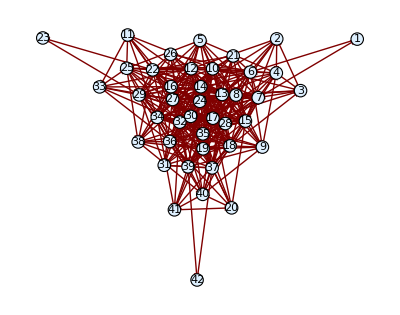
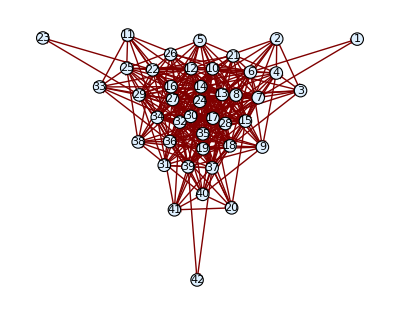
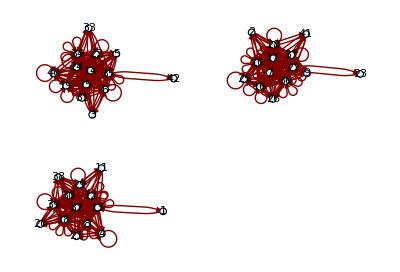
-Graphics-F_{0,0,0,0,1,0}
-Graphics-F_{1,0,0,0,0,0}
-Graphics-F_{0,0,0,0,0,1}
-Graphics-F_{0,0,0,1,0,0}
-Graphics-F_{0,1,0,0,0,0}
-Graphics-F_{0,0,1,0,0,0}

```mathematica
TableForm[Table[Magnify[Labeled[Framed[GraphPlot[ fusionmatrixlist[[s]], VertexRenderingFunction -> ({LightBlue, EdgeForm[Black], Disk[#,.10], Black, Text[#2,#1]}&) , DirectedEdges -> True, MultiedgeStyle->True,SelfLoopStyle->True],Background->LightPurple],Text[Subscript["F",Irreplist[k][[s]]],BaseStyle->{Larger}]   , Left,ImageSize-> Full],magnifactor],{s,basicpositions }]]
```

```mathematica
EdgeRenderingFunction->({Red,Arrow[#1,0.1]}&)
```

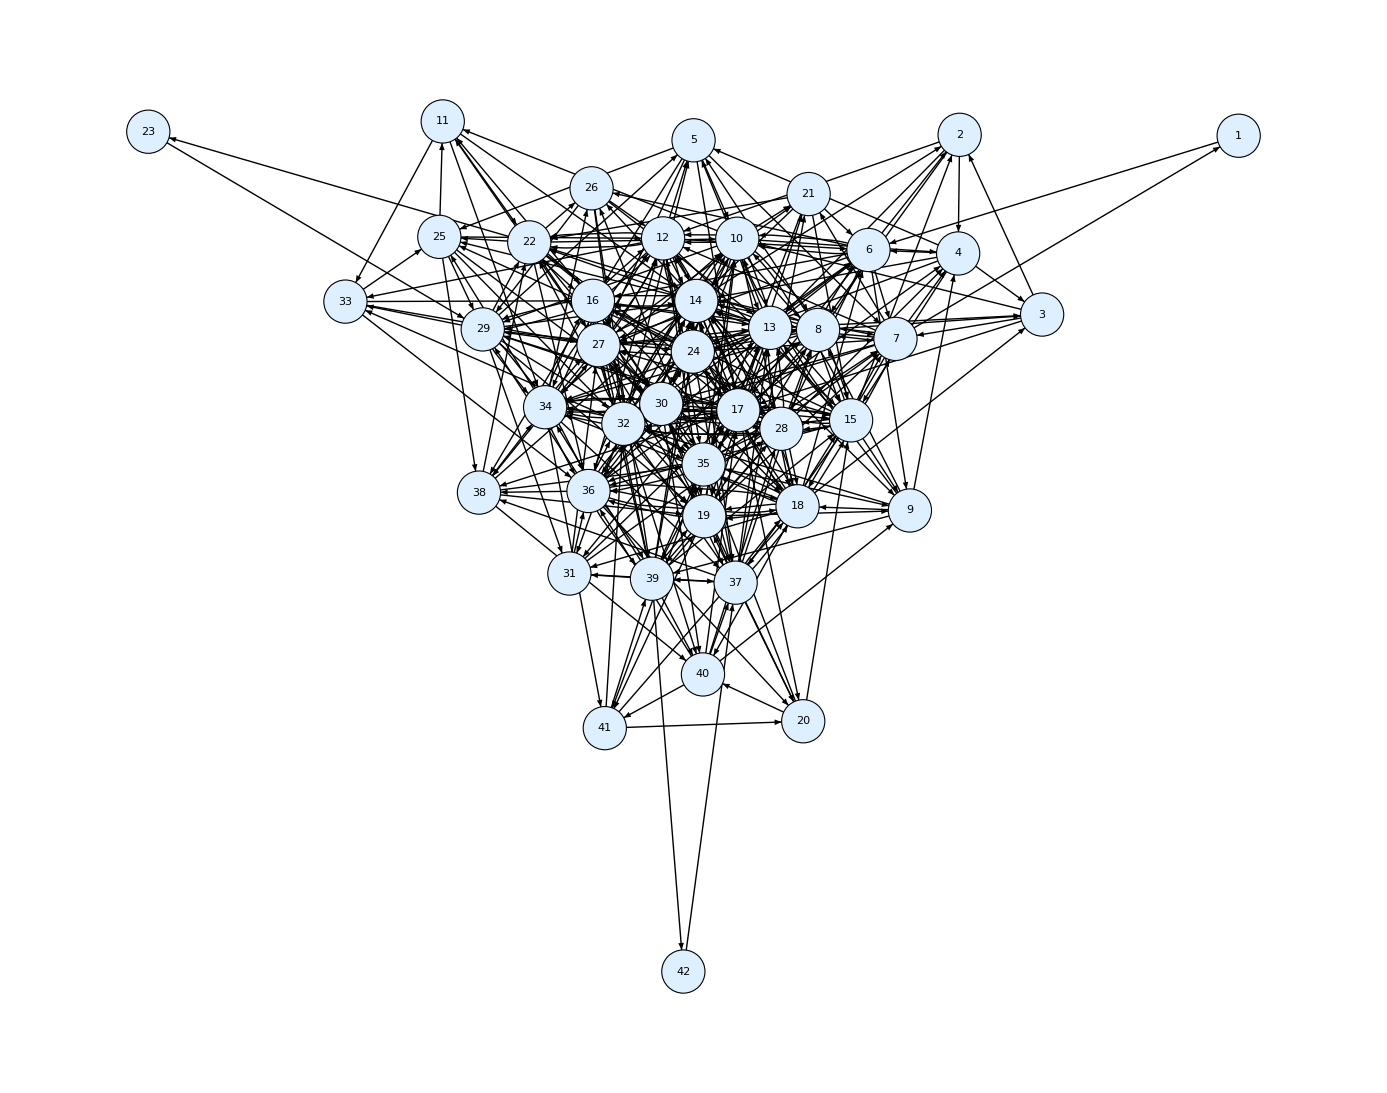

```mathematica
GraphPlot[ fusionmatrixlist[[6]], VertexRenderingFunction -> ({LightBlue, EdgeForm[Black], Disk[#,.10], Black, Text[#2,#1]}&) , DirectedEdges -> True, MultiedgeStyle->True,SelfLoopStyle->True,EdgeRenderingFunction->({Black,{Arrowheads[Small],Arrow[#1,0.1]}}&)]
```

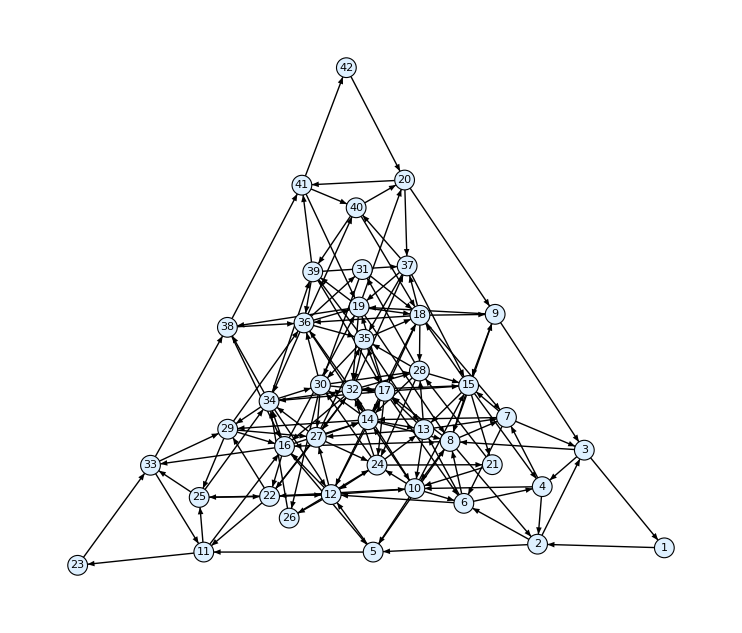

```mathematica
GraphPlot[ fusionmatrixlist[[2]], VertexRenderingFunction -> ({LightBlue, EdgeForm[Black], Disk[#,.10], Black, Text[#2,#1]}&) , DirectedEdges -> True, MultiedgeStyle->True,SelfLoopStyle->True,EdgeRenderingFunction->({Black,{Arrowheads[Small],Arrow[#1,0.1]}}&)]
```

## Clearing variables

```mathematica
Clear[horizontaldimensions,totalhorizontaldimension, bialgebradimension,fusiontitle,  integrableweightslabel, quantumgroupoidlabel, integrablefundamentalweightslabel]
```